Rabi oscillations for a two level atom with finite detuning:

```mathematica
Clear[Δ,Ω]
```

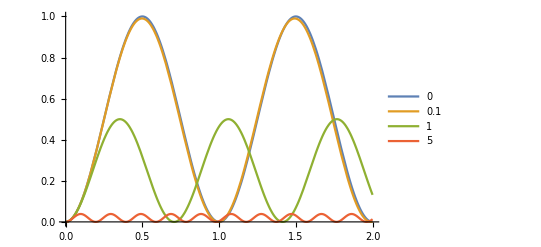

```mathematica
Pe=Ω^2/(Ω^2+Δ^2)Sin[(√(Ω^2+Δ^2))/2 t]^2;
det={0,0.1,1,5};
Plot[Evaluate[Table[Pe/.{Ω->2π},{Δ,2π*det}]],{t,0,2},PlotLegends->det]
```

Resonance experiment, scanning the over the detuning using a fixed rotation time and Rabi frequency:

```mathematica
Pe/.{Δ->0,Ω->1,t->π}
```

1

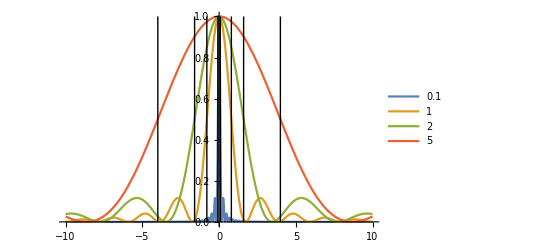

```mathematica
Rabi={0.1,1,2,5};
α=0.7986853552847012;
vlines=Table[{Line[{{-α Ω,0},{-α Ω,1}}],Line[{{α Ω,0},{α Ω,1}}]},{ Ω,Rabi}];
Plot[Evaluate[Table[Pe/.t->π/Ω,{Ω,Rabi}]],{Δ,-10,10},PlotLegends->Rabi,PlotRange->All,Epilog->vlines]
```

I worked out that the full-width at half-max (FWHM) of the power-broadened line is exactly 2*0.8 Ω or about 2 Ω. The broadening can be thought about as follows: the larger the Rabi frequency (which scales as the square root of the power), the faster the population is transferred, and the closer we get to full population transfer at finite detuning. Ω >> Δ gives near perfect transfer, as this is really a competition between these rates. For a fixed rotation time tπ = π/Ω, the pulse will fully transfer population at 0 detuning. If we now have finite detuning, we will not get full population transfer. But as we crank up Ω, we will get transfer more quickly. So the line shape will still decay toward zero as we increase detuning, but if Ω is increased, the effect is that more population is transferred even farther from resonance, which is to say the line is broadened.

```mathematica
Pe/.{Ω->1,t->π,Δ->α}
```

0.5

x = Ω/(√(Ω^2+Δ^2)) below, and the equation results from setting the population Pe = 1/2. We can find x, then solve for Δ to get the linewidth.

```mathematica
NSolve[1-1/x^2==Cos[π/x],x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[1-1/x^2==Cos[π/x],x]

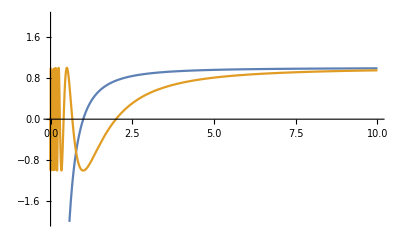

```mathematica
Plot[{1-1/x^2,Cos[π/x]},{x,0,10},PlotRange->{-2,2}]
```

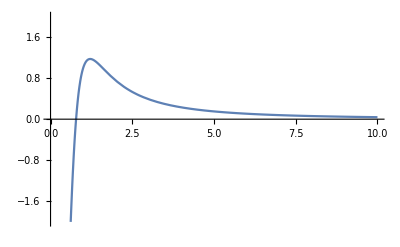

```mathematica
Plot[1-1/x^2-Cos[π/x],{x,0,10},PlotRange->{-2,2}]
```

```mathematica
f=1-1/x^2-Cos[π/x];
df=D[f,x];
```

```mathematica
xi=0.75;
```

```mathematica
xii=xi-(f/.x->xi)/(df/.x->xi)
xi=%;
```

0.78137

```mathematica
0.7790030431055457
```

0.779003

```mathematica
f/.x->xi
```

-7.77156×10^-16

```mathematica
√((1-xi^2)/xi^2)
```

0.798685